MSc Computational Physics AUTH
Subject: Computational Nuclear Physics
Academic Year: 2023-2024
Semester 2
Implemented by: Ioannis Stergakis
AEM: 4439

# PROJECT #1: Estimating parameters of the potential in deuterium nucleus Mathematica Notebook

## 1. Preliminary Theoretical Work

```mathematica
Clear["Global`*"]
```

### 1.1 Defining the wavefuction η(r) of deuterium nucleus

The wavefunction of deuterium nucleus η(r) is a piecewise function. That is, it’s formula change as we move in the r-axis, as shown below:

```mathematica
η[r_,L_]:= Piecewise[ {{A*Sin[k*r],0<=r<=L},{B*Exp[-γ*r],r>=L}}]
η[r,L]
k2 = 2m(Vo-Abs[Ed])/ℏ^2
γ2 = 2m Abs[Ed]/ℏ^2
```

Piecewise[{{A Sin[k r], 0≤r≤L}, {B ⅇ^(-r γ), r≥L}, {0, True}}]

(2 m (Vo-Abs[Ed]))/ℏ^2

(2 m Abs[Ed])/ℏ^2

### 1.2 Defining useful constants

```mathematica
hbarc=197.327  (* hbar*c product in MeV*fm *)
mnc=939.5654133 (* neutron mass in MeV *)
mpc=938.2720881 (* proton mass in MeV *)
Rd= 2.12799 (* charge radius of deuterium nucleus in fm*)
Ebnd = 2.22452 (* Absolute binding energy in deuterium nucleus in MeV*)
```

197.327

939.565

938.272

2.12799

2.22452

### 1.3 Defining the ν(ξ) functions

Requiring the continuity of the wave function η(r) and its first derivative .08ή(r) at the point r=L, we result at the following two functions, ν1(ξ) and ν2(ξ):

```mathematica
(* Definition of ν1(ξ)=-ξ*cot(ξ) as a function of ξ *)
ν1[ξ_]:=-ξ*Cot[ξ]
ν1[ξ]

(* Definition of ν2(ξ)=sqrt((2μVo/hbar^2)*L^2-ξ^2)as a function of ξ, 
Vo (potential's depth), L (potential's range) and μ (nucleon's mass)*)
ν2[ξ_,Vo_,L_,mc_]:=Sqrt[(L^2)*(2*mc*Vo)/(hbarc^2) - ξ^2]
ν2[ξ,Vo,L,μ]/.hbarc->ℏ

(* Same as ν2(ξ) but now as a function of ξ, 
VoL product (VoL = Vo*L^2) and μ (nucleon's mass) *)
ν3[ξ_,VoL_,mc_]:=Sqrt[(2*mc*VoL)/(hbarc^2)-ξ^2]
```

-ξ Cot[ξ]

√(-ξ^2+(2 L^2 Vo μ)/ℏ^2)

### 1.4 Finding the Vo*L^2 product bounds

Since cot(ξ) becomes zero at ξ = (2n+1)π/2, in order to get only one bound state (practically the ground state of deuterium nucleus), the product Vo*L^2 must be within the following bounds:

```mathematica
(* Lower Bound *)
VoLlow[mc_]:=(Pi*hbarc)^2/(8*mc)
(*  Upper Bound *)
VoLup[mc_]:= 9*(Pi*hbarc)^2/(8*mc)
VoLlow[μ]/.hbarc->ℏ
VoLup[μ]/.hbarc->ℏ
(* Considering neutron mass *)
VoLlow[mnc]
VoLup[mnc]
(* Considering proton mass *)
VoLlow[mpc]
VoLup[mpc]
```

(π^2 ℏ^2)/(8 μ)

(9 π^2 ℏ^2)/(8 μ)

(hbarc^2 π^2)/(8 mnc)

(9 hbarc^2 π^2)/(8 mnc)

(hbarc^2 π^2)/(8 mpc)

(9 hbarc^2 π^2)/(8 mpc)

### 1.4 Defining the binding energy E and parameters Vo, L functions

The binding energy E and the potential’s range L are given by the following formulas:

```mathematica
(* Defining E as function of Vo (potential's depth), L (potential's range), ξ1 (results from ν1(ξ)==ν2(ξ)) and μ (nucleon's mass) *)
Enrg[Vo_,L_,ξ1_,mc_]:=Vo - ((ξ1*hbarc)^2)/(2*mc*L^2)
Enrg[Vo,L,ξ,μ]/.hbarc->ℏ

(* Defining V as a function of Vo*L^2 product and L (potential's range) *)
V[p_,L_] :=p/(L^2) 

(* Defining L^2 as function of Vo*L^2 product, ξ1 (results from ν1(ξ)==ν3(ξ)) and μ (nucleon's mass) *)
Lsq[prod_,ξ1_,mc_] :=(prod - (hbarc^2)*(ξ1^2)/(2*mc))*(1/Abs[Ebnd]) 
Lsq[p,ξ,μ]/.hbarc->ℏ
```

Vo-(ξ^2 ℏ^2)/(2 L^2 μ)

(p-(ξ^2 ℏ^2)/(2 μ))/Abs[Ebnd]

### 1.5 Finding Energy E

Therefore, we solve the equation ν1(ξ)=ν2(ξ) to acquire ξ and then we substitute this value in the formula for the binding energy, as shown below:

```mathematica
FindEnrg[Vo_,L_,mc_,ξο_]:=Module[{result},
rootξ = FindRoot[ν1[ξ]==ν2[ξ,Vo,L,mc],{ξ,ξο}];
ξ1 = ξ/.rootξ[[1]];
If[Im[ξ1]<=0.001,ξ1=Re[ξ1]];
result = Enrg[Vo,L,ξ1,mc]
]
```

In some next functions we do the same for the potential’s range L, by solving the equation ν1(ξ)=ν3(ξ).

Notice that we need a single solution of the respective equations, to obtain only one bound state, i.e. the ground state of the deuterium nucleus. That is, a single interscection point (if such exists) for the plots of ν1(ξ) and v2(ξ) (or ν1(ξ) and v3(ξ)).

## 2. Plotting ν1(ξ), ν2(ξ) and v3(ξ)

### 2.1 Plotting ν1(ξ) and ν2(ξ)

On a first approach, one can scan an area of L (with step dL) and an area of Vo (with step dVo) and draw the plots of the function ν2(ξ) that correspond to a valid value of the product Vo*L^2, i.e. inside the bounds. The plot of v1(ξ) should also be included to confirm the single intersection case. To do so, we define the following function/module:

```mathematica
plotν12[Vomin_,Vomax_,dVo_,Lmin_,Lmax_,dL_,mc_]:=Module[{result},
plotlistv2 = {}; (*initializing a list for the plots of v2(ξ) functions*)
l=0; (*initializing counter for L<=Rd cases*)
u=0; (*initializing counter for L>Rd cases*)
tot=0; (*intializing counter for the total cases of valid product Vo*L^2, i.e inside the bounds*)

(*Scanning the given area of L - [Lmin,Lmax]*)
For[L=Lmin,L<=Lmax,L=L+dL,
(*Scanning the given area of Vo - [Vo_min,Vo_max]*)
For[Vo=Vomin,Vo<=Vomax,Vo=Vo+dVo,
VoL = Vo*L^2; (*calculating product Vo*L^2*)
If[VoL>=VoLlow[mc]&&VoL<=VoLup[mc],
tot = tot+1; (*increasing total valid cases counter by 1*)
If[L<=Rd,
l=l+1; (*increasing counter for L<=Rd cases by 1*)
plotν2 = Plot[ν2[ξ,Vo,L,mc],{ξ,Pi/2-0.5,5*Pi/2},PlotRange->{{Pi/2-0.5,5*Pi/2},{0,5}},PlotStyle->{Dashed,Green},Frame->True],
u=u+1; (*increasing counter for L>Rd cases by 1*)
plotν2 = Plot[ν2[ξ,Vo,L,mc],{ξ,Pi/2-0.5,5*Pi/2},PlotRange->{{Pi/2-0.5,5*Pi/2},{0,5}},PlotStyle->{Dashed,Orange},Frame->True]];
AppendTo[plotlistv2,plotν2](*appending the v2(ξ) to the storage list*)
]
]
];

lowperc=N[100*(l/tot)]; (*calculating the percentage of L<=Rd cases to the total valid cases*)
upperc=N[100*(u/tot)]; (*calculating the percentage of L>Rd cases to the total valid cases*)
plotν1 = Plot[ν1[ξ],{ξ,Pi/2-0.5,5*Pi/2},PlotRange->{{Pi/2-0.5,5*Pi/2},{0,5}},
PlotLegends->{"Vo: ["<>ToString[Vomin]<>","<>ToString[Vomax]<>"] MeV\ndVo: "<>ToString[dVo]<>" ΜeV\n"<>"L: ["<>ToString[Lmin]<>","<>ToString[Lmax]<>"] fm\ndL: "<>ToString[dL]<>" fm\n"<>"L<=Rd cases ("<>ToString[l]<>" - "<>ToString[lowperc]<>"%)\nL>Rd cases ("<>ToString[u]<>" - "<>ToString[upperc]<>"%)\nTotal valid cases: "<>ToString[tot]},PlotStyle->{Black},Frame->True];
result = Show[plotν1,plotlistv2,PlotLabel->"Plotting ν1(ξ) [Black] and ν2(ξ) [Green: L<=Rd, Orange: L>Rd]"]
]
```

We have the following example:

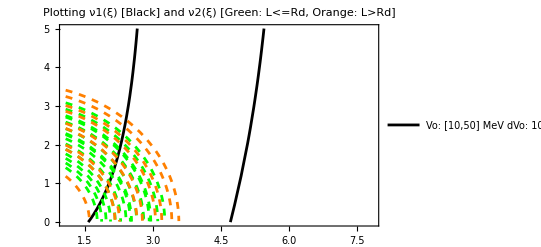

```mathematica
plotν12[10,50,10,1.8,2.3,0.1,mnc]
```

### 2.2 Plotting ν1(ξ) and ν3(ξ)

On a second approach, one can divide the valid area of the product Vo*L^2, i.e the area between the bounds, into M-1 equally lengthed intervals and draw the plots of the function ν3(ξ) corresponding to the M points, the ones that contain the valid values
of the product Vo*L^2. In this way, the user can scan the whole valid area and not just a fraction of it, like in the plotν12 module. Once again, the plot of v1(ξ) should be included to confirm the single intersection case. All the above can be achieved, by using the following function/module:

```mathematica
plotν13[M_,mc_]:=Module[{result},
dVoL = (VoLup[mc]-VoLlow[mc])/(M-1); (*dividing the valid area of the product Vo*L^2 into M-1 intervals, with equal length dVoL*);
plotlistν3 = {}; (*initializing a list for the plots of v3(ξ) functions*)

For[VoL=VoLlow[mc],VoL<=VoLup[mc],VoL=VoL+dVoL,
r = RandomReal[]; (*generating a random number for the red index in RGB color codex*)
g = RandomReal[]; (*generating a random number for the green index in RGB color codex*)
b = RandomReal[]; (*generating a random number for the blue index in RGB color codex*)
plotν3 = Plot[ν3[ξ,VoL,mc],{ξ,Pi/2-0.5,5*Pi/2},PlotRange->{{Pi/2-0.5,5*Pi/2},{0,5}},PlotStyle->{Dashed,RGBColor[r,g,b]},PlotLegends->{"ν3(ξ) -> VoL = "<>ToString[VoL]<>" ΜeV*fm^2"}];
AppendTo[plotlistν3,plotν3] (*appending the v3(ξ) plot to the storage list*)
];

plotν1 = Plot[ν1[ξ],{ξ,Pi/2-0.5,5*Pi/2},PlotRange->{{Pi/2-0.5,5*Pi/2},{0,5}},PlotStyle->{Black},PlotLegends->{"ν1(ξ)"},AxesLabel->{"ξ","ν(ξ)"},Frame->True];
result = Show[plotν1,plotlistν3,PlotLegends->Automatic,PlotLabel->"Plotting ν1(ξ) and ν3(ξ)"]
]
```

We have the following example:

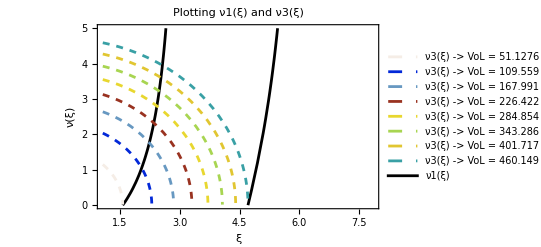

```mathematica
plotν13[8,mnc]
```

## 3. Estimating and illustrating the best values for the parameters Vo and L

### 3.1 Estimation and illustration using values seperately for Vo and L

Another useful investigation for the Deuterium problem, can be mabe by scanning a specific area in the Vo - L space,
and determine which points (L,Vo) give a value for the product Vo*L^2 that is valid (i.e lies between the bounds). Also, for a single point (L,Vo), we can examine if the respective calculated value for the binding energy (Ecalc) is close to the actual value (Ebnd) of deuterium’s binding energy and if the value of L is close to the value of deuterium’s radius. Finally, for better understanding we can draw all these points in the Vo-L space, using different colors, depending on the case, along with the curves that represent the bounds of the Vo*L^2 product.  

Thus, we define the following function/module, where Vomin and Vomax are the scanning bounds-to-be-selected for Vo and Lmin and Lmax are the respective bounds for L. The values dVo and dL represent the step for the scan of Vo-axis and L-axis, respectively. Finally, tol is the tolerance for the error of the binding energy calculation and Rdist the maximum accepted difference between one point’s L value and deuterium’s radius.

```mathematica
est1VoL[Vomin_,Vomax_,dVo_,Lmin_,Lmax_,dL_,mc_,tol_,Rdist_]:=Module[{result},
listout = {}(*initializing a list to storage the points [L,Vo] that lie outside the valid area*);
listin = {}; (*initializing a list to storage the points [L,Vo] that lie inside the valid area*)
listinacc = {}; (*initializing a list to storage the valid points [L,Vo], that result also to an accurate value of the binding energy*)
listinaccnear = {}; (*initializing a list to storage the valid points [L,Vo] with an accurate value of the binding energy, that have a value of L close to Rd, i.e a distance from Rd less than Rdist fm*)
out = 0; (*counter of the non-valid points [L,Vo]*)
in = 0; (*counter of all valid points [L,Vo]*)
inacc = 0; (*counter of the valid points [L,Vo], with an accurate value of the binding energy*)
inaccnear = 0; (*counter of the valid points [L,Vo] with accurate value of the binding energy and a value of L close to Rd*)
tot = 0;(*counter of the total points [L,Vo]*)

(*Scanning the given area of L - [Lmin,Lmax]*)
For[L=Lmin,L<=Lmax,L=L+dL,
(*Scanning the given area of Vo - [Vo_min,Vo_max]*)
For[Vo=Vomin,Vo<=Vomax,Vo = Vo + dVo,
tot = tot+1;
VoL = Vo*L^2;
If[VoL< VoLlow[mc]||VoL>VoLup[mc],out = out + 1;AppendTo[listout,{L,Vo}],
in = in +1;
(*Binding energy calculation*)
Ecalc = FindEnrg[Vo,L,mc,Pi/2];
(*et: true percent relative error in binding energy calculation*)
et = 100*Abs[(Ebnd - Ecalc)/Ebnd];
If[et>tol,AppendTo[listin,{L,Vo}],
inacc = inacc +1;
If[Abs[Rd-L]<=Rdist,inaccnear = inaccnear+1;AppendTo[listinaccnear ,{L,Vo}],AppendTo[listinacc,{L,Vo}]]
]
]
]
];

percout = N[100*out/tot];(*percentage of points outside the valid area*)
percin = N[100*in/tot];(*percentage of points inside the valid area*)
percinacc = N[100*inacc/tot]; (*percentage of valid points with accurate binding energy*)(*percentage of valid points with accurate binding energy and close to Rd*)
percinaccnear = N[100*inaccnear/tot];
(*Printing the results*) 
Print["---------------------------------------------"];
Print["SUMMARY OF CALCULATIONS:\n"];
Print["Total cases: ",tot];
Print["OUT-OF-BOUND cases: ",out," (",percout,"%)"];
Print["IN-BOUND cases: ",in," (",percin,"%)"];
Print["IN-BOUND and ACCURATE cases: ",inacc," (",percinacc,"%)"];
Print["IN-BOUND, ACCURATE and NEAR cases: ",inaccnear," (",percinaccnear,"%)"];
Print["---------------------------------------------"];

(*Plotting the scatter diagram of the non-valid points*)
plotout = ListPlot[{listout},PlotLabel->"Potential's depth Vo and range L scatter diagram",PlotStyle->{Gray},Frame->True,GridLines->Automatic,
PlotLegends->{"OUT-OF-BOUND (VoL<lowbnd or VoL>upbnd)\n"<>ToString[out]<>" cases - "<>ToString[percout]<>"%"}];
(*Plotting the scatter diagram of all valid points*)
plotin = ListPlot[{listin},PlotStyle->{Red},Frame->True,GridLines->Automatic,
PlotLegends->{"IN-BOUND (VoL>=lowbnd and VoL<=upbnd)\n"<>ToString[in]<>" cases - "<>ToString[percin]<>"%"}];
(*Plotting the scatter diagram of the valid points with accurate binding energy*)
plotinacc = ListPlot[{listinacc},PlotStyle->{Yellow},Frame->True,GridLines->Automatic,
PlotLegends->{"IN-BOUND and ACCURATE (et<="<>ToString[tol]<>"%)\n"<>ToString[inacc]<>" cases - "<>ToString[percinacc]<>"%"}];
(*Plotting the scatter diagram of the valid points with accurate binding energy and L close to Rd*)
plotinaccnear = ListPlot[{listinaccnear },PlotStyle->{Green},Frame->True,GridLines->Automatic,
PlotLegends->{"IN-BOUND, ACCURATE (et<="<>ToString[tol]<>"%)\nand NEAR (|Rd-L|<="<>ToString[Rdist]<>"fm)\n"<>ToString[inaccnear]<>" cases - "<>ToString[percinaccnear]<>"%"}];
(*Plotting the curve of the lower bound, i.e. the curve Vo = VoL_low/L^2*)
plotlowbnd =  Plot[V[VoLlow[mc],L],{L,Lmin-0.1,Lmax+0.1},PlotStyle->{Purple},AxesLabel->{"L (fm)","Vo (MeV)"},PlotLegends->{"Lower Bound: Vo = a/L^2 (a = "<>ToString[VoLlow[mc]]<>" MeV*fm^2)"} ];
(*Plotting the curve of the upper bound, i.e. the curve Vo = VoL_up/L^2*)
plotupbnd =  Plot[V[VoLup[mc],L],{L,Lmin-0.1,Lmax+0.1} ,PlotLegends->{"Upper Bound: Vo = a/L^2 (a = "<>ToString[VoLup[mc]]<>" MeV*fm^2)"}];
result = Show[plotout,plotin,plotinacc,plotinaccnear,plotlowbnd,plotupbnd ,PlotRange->All,AxesLabel->Automatic]
]
```

We have the following example:

---------------------------------------------

SUMMARY OF CALCULATIONS:

Total cases: 12880

OUT-OF-BOUND cases: 10248 (79.5652%)

IN-BOUND cases: 2632 (20.4348%)

IN-BOUND and ACCURATE cases: 52 (0.403727%)

IN-BOUND, ACCURATE and NEAR cases: 52 (0.403727%)

---------------------------------------------

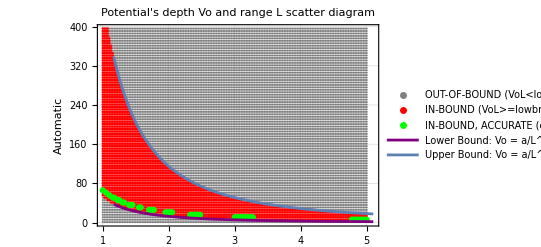

```mathematica
est1VoL[1,400,5,1,5,0.025,mnc,20,3]
```

### 3.2 Estimation and illustration using values of the product Vo*L^2

We can also perform a scan, limited only in the valid area of the product Vo*L^2.  To do so we need to select a number of points M in this area. For each of these points, we check if the value of L is imaginary or real, an then if L is close to deuteron’s radius, that is if the difference |Rd-L| is less or more than 2fm.

```mathematica
est2VoL[M_,mc_]:=Module[{result},
If[M<2,M=2]; (* Ensure at least two points are selected in the valid area of the product Vo*L^2*)
listnear = {}; (* initializing a list to store the valid points [L,Vo] that have a value of L close to Rd, i.e a distance from Rd less than  2fm *)
listfar= {}; (* initializing a list to store the valid points [L,Vo] that have a value of L far from Rd, i.e a distance from Rd more than  2fm *)
(*calculating the step of the product Vo*L^2 based on the selected points M*)
dVoL = (VoLup[mc]-VoLlow[mc])/(M-1); 
tot=0; (*counter for the total cases*)
near = 0; (*counter for the near cases, i.e |Rd-L|<=2fm*)
far = 0; (*counter for the far cases, i.e |Rd-L|>2fm*)
img = 0; (*counter of the imaginary L cases*)
Print["--------------------------------------------"];
Print["ESTIMATIONS - CALCULATIONS:\n"];
Print["Iter  p[MeV*fm^2]\tξ1\t  L(fm)\tVo(MeV)"];
Print["--------------------------------------------"];
(*Scanning the valid area*)
For[VoL=VoLlow[mc],VoL<=VoLup[mc],VoL=VoL+dVoL,
tot=tot+1;
(*Finding ξ based on the value of the product Vo*L^2*)
rootξ= FindRoot[ν1[ξ]==ν3[ξ,VoL,mc],{ξ,2}]; 
ξ1 = ξ/.rootξ[[1]];
(*In case the imaginary part of ξ is very small we consider ξ as a real and not a complex number*)
If[Im[ξ1]<=0.001,ξ1=Re[ξ1]];
L2 = Lsq[VoL,ξ1,mc];(*Calculating L^2 using the Lsq function we defined earlier*)
L1 = Sqrt[L2]; (*Calculating the value of L*)
(*Checking if L is imaginary or real*)
If[L2<0,
(*Printing the info of the current point (with imaginary L value)*) 
Print[tot,"  \t",VoL,"\t ",ξ1,"\t","img","\t\t\t","-"];
img = img + 1;
Continue,
Vo=V[VoL,L1];
(*Printing the info of the current point (with real L value)*)
Print[tot,"  \t",VoL,"\t ",ξ1,"\t",L1,"\t",Vo];
(*Checking if L (when real) is close or far from Rd*)
If[Abs[Rd-L1]<=2,AppendTo[listnear,{L1,Vo}];near=near+1,AppendTo[listfar,{L1,Vo}];far=far+1]]
];
(*Printing the results*)
Print["---------------------------------------------"];
(*Calculating the percentages of different cases*)
percnear = N[100*near/tot];(*percentage of the |Rd-L|<=2fm case*)
percfar = N[100*far/tot]; (*percentage of the |Rd-L|>2fm case*)
percimg = N[100*img/tot];(*percentage of the imaginray L case*)
Print["SUMMARY:\n"];
Print["TOTAL CASES: ",tot];
Print["NEAR CASES (|Rd-L|<=2fm): ",near,"(",percnear,"%)"];
Print["FAR CASES (|Rd-L|>2fm): ",far,"(",percfar,"%)"];
Print["IMAGINARY L CASES: ",img,"(",percimg,"%)"];
Print["---------------------------------------------\n"];
(*Plotting the points where L is close to Rd*)
plotnear = ListPlot[{listnear},PlotLabel->"Potential's depth Vo and range L scatter diagram",PlotStyle->{Green},Frame->True,GridLines->Automatic,
PlotLegends->{"|Rd-L|<=2fm\n"<>ToString[near]<>" cases - "<>ToString[percnear]<>"%"}];
(*Plotting the points where L is far from Rd*)
plotfar = ListPlot[{listfar},PlotStyle->{Red},Frame->True,GridLines->Automatic,
PlotLegends->{"|Rd-L|>2fm\n"<>ToString[far]<>" cases - "<>ToString[percfar]<>"%"}];
Show[plotnear,plotfar,PlotRange->All,AxesLabel->Automatic]
]
```

We have the following example:

--------------------------------------------

ESTIMATIONS - CALCULATIONS:

Iter  p[MeV*fm^2]	ξ1	  L(fm)	Vo(MeV)

--------------------------------------------

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

1  	51.1276	 1.5708	img			-

2  	60.4236	 1.69457	0.643442	145.944

3  	69.7195	 1.79029	1.21894	46.9233

4  	79.0154	 1.86746	1.74224	26.0313

5  	88.3114	 1.93155	2.22401	17.8543

6  	97.6073	 1.98598	2.67185	13.6728

7  	106.903	 2.03302	3.09138	11.1863

8  	116.199	 2.07424	3.48686	9.55726

9  	125.495	 2.11079	3.86164	8.41557

10  	134.791	 2.14351	4.21836	7.57484

11  	144.087	 2.17304	4.55919	6.93186

12  	153.383	 2.19988	4.88588	6.42526

13  	162.679	 2.22442	5.19993	6.01639

14  	171.975	 2.24698	5.50257	5.67981

15  	181.271	 2.26783	5.79486	5.3981

16  	190.567	 2.28717	6.07772	5.15899

17  	199.863	 2.30518	6.35194	4.95358

18  	209.159	 2.32201	6.61819	4.77526

19  	218.454	 2.33779	6.8771	4.61903

20  	227.75	 2.35262	7.12918	4.48105

21  	237.046	 2.3666	7.37492	4.35831

22  	246.342	 2.37981	7.61474	4.24843

23  	255.638	 2.39232	7.84902	4.14949

24  	264.934	 2.40419	8.0781	4.05993

25  	274.23	 2.41547	8.3023	3.97849

26  	283.526	 2.42621	8.52188	3.90411

27  	292.822	 2.43646	8.73712	3.8359

28  	302.118	 2.44625	8.94823	3.77313

29  	311.414	 2.45561	9.15544	3.71518

30  	320.71	 2.46459	9.35894	3.6615

31  	330.006	 2.47319	9.55891	3.61164

32  	339.302	 2.48145	9.75553	3.56521

33  	348.598	 2.4894	9.94893	3.52185

34  	357.893	 2.49704	10.1393	3.48129

35  	367.189	 2.50441	10.3267	3.44324

36  	376.485	 2.51151	10.5113	3.40749

37  	385.781	 2.51837	10.6932	3.37383

38  	395.077	 2.52499	10.8726	3.34208

39  	404.373	 2.5314	11.0494	3.31208

40  	413.669	 2.53759	11.2239	3.2837

41  	422.965	 2.54359	11.3961	3.2568

42  	432.261	 2.5494	11.5661	3.23127

43  	441.557	 2.55504	11.7339	3.207

44  	450.853	 2.56051	11.8997	3.18391

45  	460.149	 2.56582	12.0635	3.16191

---------------------------------------------

SUMMARY:

TOTAL CASES: 45

NEAR CASES (|Rd-L|<=2fm): 8(17.7778%)

FAR CASES (|Rd-L|>2fm): 36(80.%)

IMAGINARY L CASES: 1(2.22222%)

---------------------------------------------

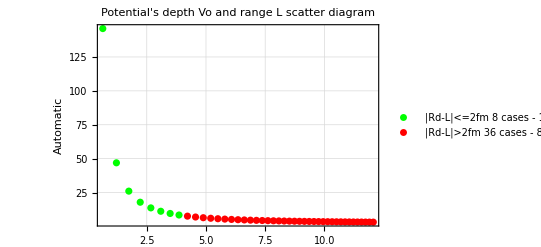

```mathematica
est2VoL[45,mnc]
```

## 4. Plotting the wavefunction η(r) and the probability p(r)

```mathematica
plotwf[Vo_,L_,rmin_,rmax_,mc_,tolE_,tolR_]:= Module[{result=0},
(*Calculating the product Vo*L^2 from the given values of Vo and L*)
VoL = Vo*L^2;

(*Checking if the value of Vo*L^2 is valid*)
If[VoLlow[mc]<=VoL<=VoLup[mc],(*valid case*)
Ecalc = FindEnrg[Vo,L,mc,Pi/2];(*Calculating the binding energy*)
(*Calculating the error in binding energy's calculation *)
etE = 100*Abs[(Ebnd - Ecalc)/Ebnd];
(*Calculating the k and γ parameters of the wavefucntion η(r)*)
k = Sqrt[2*mc*(Vo-Ecalc)/(hbarc^2)];
γ = Sqrt[2*mc*Ecalc/(hbarc^2)];
(*Calculate the integral of (η(r)/A)^2 in the area [0,L]*)
I1= Integrate[(Sin[k*r])^2,{r,0,L}];
(*Calculate the integral of (η(r)/B)^2 in the area [L,infinity]*)
I2 = Integrate[Exp[-2*γ*r],{r,L,Infinity}];
(*Calculating the value of the C1 constant from the continuity equation of η(r)*)
(*C1 = B/A and the continuity equation A*sin(kL)=B*exp(-γL) becomes C1=sin(kL)*exp(γL)*)
C1 = Sin[k*L]*Exp[γ*L];
C2 = C1^2; (*So C2 = (B/A)^2 => B^2 = C2*A^2*)
(*The proper normalization of η(r) demands that (A^2)*I1 + (B^2)*I2=1*)
A = Sqrt[1/(I1+C2*I2)];(*Calculating the A coefficient of η(r)*)
B = A*C1];(*Calculating the B coefficient of η(r)*)
(*Check for proper normalization of η(r)*)
normcheck = Integrate[η[r,L]^2,{r,0,Infinity}];
(*Calculate the mean value of r*)
meanR = Sqrt[Integrate[(η[r,L]*r)^2,{r,0,Infinity}]];
(*Finding the difference between the mean r and deuteron's radius as error*)
etR = 100*Abs[(Rd- meanR)/Rd];

If[VoL<VoLlow[mc]||VoL>VoLup[mc],(*invalid case*)
(*Plotting the function y=0 with grey color and return the plot as output of the module*)
result = Plot[0,{r,rmin,rmax},PlotRange->Full,PlotStyle->Gray,PlotLabel->"Wavefunction η(r) (OUT-OF-BOUNDS)",GridLines->Automatic,Frame->True,PlotLegends->{"Normal. Val: "<>ToString[normcheck]<>"\n<R> = -- fm\nE = -- MeV\nk = -- 1/fm\nγ = -- 1/fm"}];
Return[result],
If[etE<=tolE && etR<=tolR,(*accurate binding energy and mean r value close to deuteron's radius*)
(*Plotting the wavefunction η(r) with green color and return the plot as output of the module*)
result = Plot[η[r,L],{r,rmin,rmax},PlotRange->Full,PlotStyle->Green,PlotLabel->"Wavefunction η(r) (IN-BOUNDS, tolE = "<>ToString[tolE]<>"%, tolR = "<>ToString[tolR]<>"%)",GridLines->Automatic,Frame->True,PlotLegends->{"Normal. Val: "<>ToString[normcheck]<>"\n<R> = "<>ToString[meanR]<>" fm (err: "<>ToString[etR]<>"%)\nE = "<>ToString[Ecalc]<>" MeV (err: "<>ToString[etE]<>"%)\nk = "<>ToString[k]<>" 1/fm\nγ = "<>ToString[γ]<>" 1/fm"}];
Return[result],
If[etE<=tolE||etR<=tolR,(*accurate binding energy or mean r value close to deuteron's radius*)
(*Plotting the wavefunction η(r) with orange color and return the plot as output of the module*)
result = Plot[η[r,L],{r,rmin,rmax},PlotRange->Full,PlotStyle->Orange,PlotLabel->"Wavefunction η(r) (IN-BOUNDS, tolE = "<>ToString[tolE]<>"%, tolR = "<>ToString[tolR]<>"%)",GridLines->Automatic,Frame->True,
PlotLegends->{"Normal. Val: "<>ToString[normcheck]<>"\n<R> = "<>ToString[meanR]<>" fm (err: "<>ToString[etR]<>"%)\nE = "<>ToString[Ecalc]<>" MeV (err: "<>ToString[etE]<>"%)\nk = "<>ToString[k]<>" 1/fm\nγ = "<>ToString[γ]<>" 1/fm"}];
Return[result],
(*neither accurate binding energy nor mean r value close to deuteron's radius*)
(*Plotting the wavefunction η(r) with red color and return the plot as output of the module*)
result = Plot[η[r,L],{r,rmin,rmax},PlotRange->All,PlotStyle->Red,PlotLabel->"Wavefunction η(r) (IN-BOUNDS, tolE = "<>ToString[tolE]<>"%, tolR = "<>ToString[tolR]<>"%)",GridLines->Automatic,Frame->True,PlotLegends->{"Normal. Val: "<>ToString[normcheck]<>"\n<R> = "<>ToString[meanR]<>" fm (err: "<>ToString[etR]<>"%)\nE = "<>ToString[Ecalc]<>" MeV (err: "<>ToString[etE]<>"%)\nk = "<>ToString[k]<>" 1/fm\nγ = "<>ToString[γ]<>" 1/fm"}];
Return[result]
]
]
]
]
```

```mathematica
plotprob[Vo_,L_,rmin_,rmax_,mc_,tolE_,tolR_]:= Module[{result=0},
(*Calculating the product Vo*L^2 from the given values of Vo and L*)
VoL = Vo*L^2;

(*Checking if the value of Vo*L^2 is valid*)
If[VoLlow[mc]<=VoL<=VoLup[mc],(*valid case*)
Ecalc = FindEnrg[Vo,L,mc,Pi/2];(*Calculating the binding energy*)
(*Calculating the error in binding energy's calculation *)
etE = 100*Abs[(Ebnd - Ecalc)/Ebnd];
(*Calculating the k and γ parameters of the wavefucntion η(r)*)
k = Sqrt[2*mc*(Vo-Ecalc)/(hbarc^2)];
γ = Sqrt[2*mc*Ecalc/(hbarc^2)];
(*Calculate the integral of (η(r)/A)^2 in the area [0,L]*)
I1= Integrate[(Sin[k*r])^2,{r,0,L}];
(*Calculate the integral of (η(r)/B)^2 in the area [L,infinity]*)
I2 = Integrate[Exp[-2*γ*r],{r,L,Infinity}];
(*Calculating the value of the C1 constant from the continuity equation of η(r)*)
(*C1 = B/A and the continuity equation A*sin(kL)=B*exp(-γL) becomes C1=sin(kL)*exp(γL)*)
C1 = Sin[k*L]*Exp[γ*L];
C2 = C1^2;(*So C2 = (B/A)^2 => B^2 = C2*A^2*)
(*The proper normalization of η(r) demands that (A^2)*I1 + (B^2)*I2=1*)
A = Sqrt[1/(I1+C2*I2)];(*Calculating the A coefficient of η(r)*)
B = A*C1];(*Calculating the B coefficient of η(r)*)
(*Check for proper normalization of η(r)*)
normcheck = Integrate[η[r,L]^2,{r,0,Infinity}];
(*Calculate the mean value of r*)
meanR = Sqrt[Integrate[(η[r,L]*r)^2,{r,0,Infinity}]];
(*Finding the difference between the mean r and deuteron's radius as error*)
etR = 100*Abs[(Rd- meanR)/Rd];

If[VoL<VoLlow[mc]||VoL>VoLup[mc],(*invalid case*)
(*Plotting the function y=0 with grey color and return the plot as output of the module*)
result = Plot[0,{r,rmin,rmax},PlotRange->Full,PlotStyle->Gray,PlotLabel->"Probability p(r) (OUT-OF-BOUNDS)",GridLines->Automatic,Frame->True,PlotLegends->{"Normal. Val: "<>ToString[normcheck]<>"\n<R> = -- fm\nE = -- MeV\nk = -- 1/fm\nγ = -- 1/fm"}];
Return[result],
If[etE<=tolE&&etR<=tolR,(*accurate binding energy and mean r value close to deuteron's radius*)
(*Plotting the probability p(r) with green color and return the plot as output of the module*)
result = Plot[(η[r,L]/r)^2,{r,rmin,rmax},PlotRange->Full,PlotStyle->Green,PlotLabel->"Probability p(r) (IN-BOUNDS, tolE = "<>ToString[tolE]<>"%, tolR = "<>ToString[tolR]<>"%)",GridLines->Automatic,Frame->True,PlotLegends->{"Normal. Val: "<>ToString[normcheck]<>"\n<R> = "<>ToString[meanR]<>" fm (err: "<>ToString[etR]<>"%)\nE = "<>ToString[Ecalc]<>" MeV (err: "<>ToString[etE]<>"%)\nk = "<>ToString[k]<>" 1/fm\nγ = "<>ToString[γ]<>" 1/fm"}];
Return[result],
If[etE<=tolE||etR<=tolR,(*accurate binding energy or mean r value close to deuteron's radius*)
(*Plotting the probability p(r) with orange color and return the plot as output of the module*)
result = Plot[(η[r,L]/r)^2,{r,rmin,rmax},PlotRange->Full,PlotStyle->Orange,PlotLabel->"Probability p(r) (IN-BOUNDS, tolE = "<>ToString[tolE]<>"%, tolR = "<>ToString[tolR]<>"%)",GridLines->Automatic,Frame->True,
PlotLegends->{"Normal. Val: "<>ToString[normcheck]<>"\n<R> = "<>ToString[meanR]<>" fm (err: "<>ToString[etR]<>"%)\nE = "<>ToString[Ecalc]<>" MeV (err: "<>ToString[etE]<>"%)\nk = "<>ToString[k]<>" 1/fm\nγ = "<>ToString[γ]<>" 1/fm"}];
Return[result],
(*neither accurate binding energy nor mean r value close to deuteron's radius*)
(*Plotting the probability p(r) with red color and return the plot as output of the module*)
result = Plot[(η[r,L]/r)^2,{r,rmin,rmax},PlotRange->All,PlotStyle->Red,PlotLabel->"Probability p(r) (IN-BOUNDS, tolE = "<>ToString[tolE]<>"%, tolR = "<>ToString[tolR]<>"%)",GridLines->Automatic,Frame->True,PlotLegends->{"Normal. Val: "<>ToString[normcheck]<>"\n<R> = "<>ToString[meanR]<>" fm (err: "<>ToString[etR]<>"%)\nE = "<>ToString[Ecalc]<>" MeV (err: "<>ToString[etE]<>"%)\nk = "<>ToString[k]<>" 1/fm\nγ = "<>ToString[γ]<>" 1/fm"}];
Return[result]
]
]
]
]
```

The modules plotwf and plotprob we defined above can be used as is, to test a single combination at a time for the values of Vo and L. But they can also be used inside a manipulation command, to better see, in a more interactive way, the effect of the values Vo and L, in the behavior of the wavefunction η(r) and its probability p(r). We have the following example for the wavefunction η(r):

```mathematica
Manipulate[plotwf[Vo,L,0,10,mnc,30,30],{Vo,1,50,0.5},{L,1.5,5,0.1}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {0.224313,0,∞}.

and the following example for the probability p(r) = (η(r)/r)^2:

```mathematica
Manipulate[plotprob[Vo,L,0,10,mnc,30,30],{Vo,1,50,0.1},{L,1.5,5,0.1}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {0.224313,0,3.1}.

Integrate::ilim: Invalid integration variable or limit(s) in {0.224313,3.1,∞}.

Integrate::ilim: Invalid integration variable or limit(s) in {0.224313,0,∞}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.